### Hamiltonian: regularization of the Coulomb potential

Electronic potential energy

A parameter α is necessary to regularize the potential energy to avoid the potential energy to blow up at singularities.

```mathematica
Subscript[𝒱, e][r__,r1__,r2__,α_]:=-1/(√(Norm[{r}-{r1}]^2+α^2))-1/(√(Norm[{r}-{r2}]^2+α^2))
```

Nuclear potential energy

```mathematica
Subscript[𝒱, n][r1__,r2__]:=1/Norm[{r2}-{r1}]
```

Kinetic energy operator:

```mathematica
𝒦(ψ_)(r__):=-1/2 ψ(r){r}
```

Electronic Hamiltonian operator:

```mathematica
Subscript[ℋ, e][ψ_][r__,r1__,r2__,α_]:=ψ[r] Subscript[𝒱, e][r,r1,r2,α]+𝒦[ψ][r]
```

### Eigensystem for the left(right) system

The function eigensystem[l,𝓇,ne], finds ne eigenvalues of the H_2^+ for a internuclear distance 𝓇 in a computational box of length 2ℓ+𝓇 :

```mathematica
esysLR[ℓ_,𝓇_,ne_,a_]:=
SortBy[
Transpose[
NDEigensystem[{Subscript[ℋ, e][ψ][x,-𝓇/2,𝓇/2,a],DirichletCondition[ψ[x]==0,True]},ψ,
{x,𝓇/2,ℓ},ne,Method-> {"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.01}}}}]],
First]
```

```mathematica
eLR1=esysLR[40.,1.,60,0.001];
```

```mathematica
eLR1[[1]]
```

{-0.968488,InterpolatingFunction[{{0.5, 40.}}, <>]}

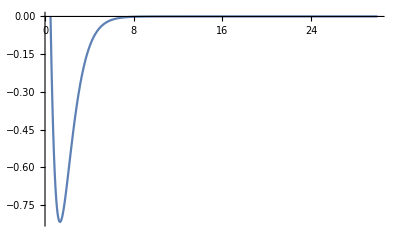

```mathematica
Plot[{eLR1[[1,2]][x]},{x,0.5,30},PlotRange->All]
```

### Eigensystem for the central system

```mathematica
esysC[𝓇_,ne_,a_]:=
SortBy[
Transpose[
NDEigensystem[{Subscript[ℋ, e][ψ][x,-𝓇/2,𝓇/2,a],DirichletCondition[ψ[x]==0,True]},ψ,
{x,-𝓇/2,𝓇/2},ne,Method-> {"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.01}}}}]],
First]
```

```mathematica
eC1=esysC[3,60,0.01];
```

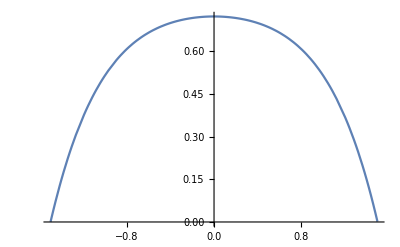

```mathematica
Plot[{eC1[[1,2]][x]},{x,-30,30},PlotRange->All]
```

#### Matching the three solutions

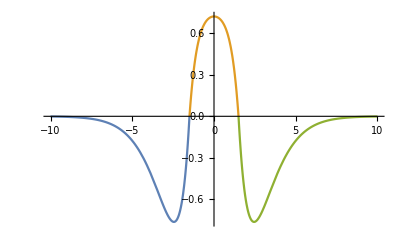

```mathematica
Plot[{eLR1[[1,2]][-x],eC1[[1,2]][x],eLR1[[1,2]][x]},{x,-10,10.},PlotRange->All]
```

#### The ground state energies as function of the internuclear distance for left-right and central systems

```mathematica
eLR[r_]:=esysLR[40.1,r,60,0.001]
```

```mathematica
eC[r_]:=esysC[r,60,0.001]
```

```mathematica
eLRC=Table[{r,eLR[r],eC[r]},{r,1.0,18.2,0.1}];
```

#### Interpolating the eigenstates as functions of r

```mathematica
eLRr=Table[Interpolation[Table[{eLRC[[i,1]],eLRC[[i,2,j,1]]},{i,1,Length[eLRC]}]],{j,1,10}];
```

```mathematica
eCr=Table[Interpolation[Table[{eLRC[[i,1]],eLRC[[i,3,j,1]]},{i,1,Length[eLRC]}]],{j,1,10}];
```

For the LR system

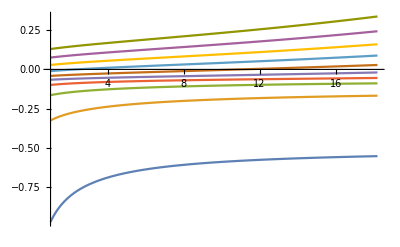

```mathematica
plotLR=Plot[Evaluate@Table[eLRr[[i]][x],{i,1,10}],{x,1,18.2},PlotRange->All]
```

The indexing is given by this example

first index is the bond length
second index is 1 for bond length, 2 for LR, and 3 for C
third index is the eigenstate
fourth index is 1 for the eigenvalue and 2 for the wave function

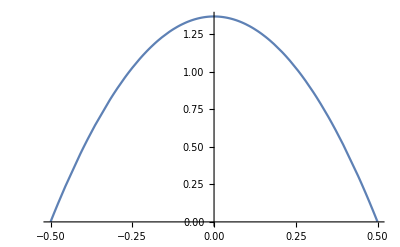

```mathematica
Plot[eLRC[[1,3,1,2]][x],{x,-0.5,18},PlotRange->All]
```

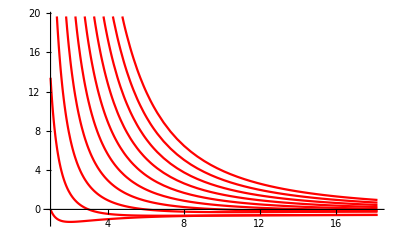

```mathematica
plotC=Plot[Table[eCr[[i]][x],{i,1,10}],{x,1,18.2},PlotStyle->Red]
```

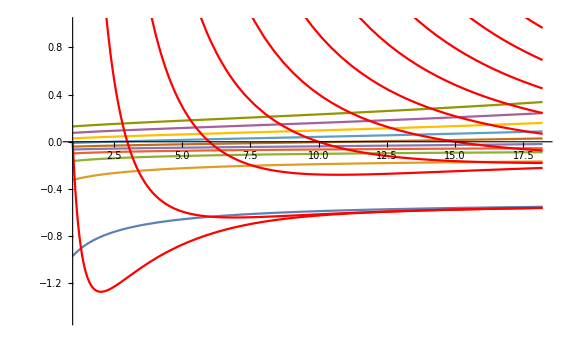

```mathematica
Show[plotLR,plotC,PlotRange->{-1.5,1}]
```

#### Intersection between curves gives good Born-Oppenheimer states

For the ground state:

```mathematica
(*ground={r,eLRr[[1]][r],eLR[y]/.y->r,eC[r]}*)
root=r/.FindRoot[Evaluate[eCr[[1]][r]]==Evaluate[eLRr[[1]][r]],{r,1}];
```

```mathematica
ground=Evaluate[{root,eLRr[[1]][root],eLR[root],eC[root]}];
```

Plotting the wave function

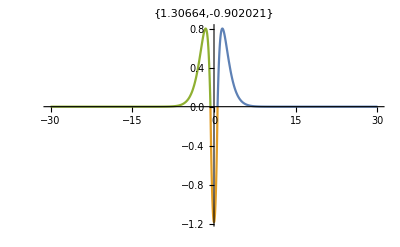

```mathematica
Plot[Evaluate@{ground[[3,1,2]][x],ground[[4,1,2]][x],ground[[3,1,2]][-x]},{x,-30,30},PlotRange->All,PlotLabel->{ground[[1]],ground[[2]]}]
```

It is seen that the derivative of the wave function has a discontinuity at the position of the nuclei.

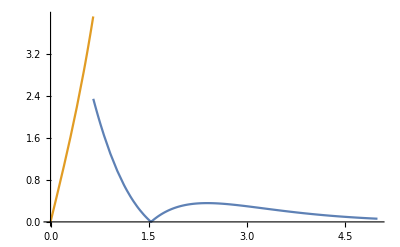

```mathematica
Plot[{Abs[D[ground[[3,1,2]][r],r]]/.r->y,Abs[D[ground[[4,1,2]][r],r]]/.r->y},{y,0,5},PlotRange->All]
```

```mathematica
dgC=Abs[D[ground[[4,1,2]][x],x]]/.x->ground[[1]]/2
```

3.91432

```mathematica
dgLR=Abs[ground⟦3,1,2⟧'[ground⟦1⟧/2]]
```

2.34513

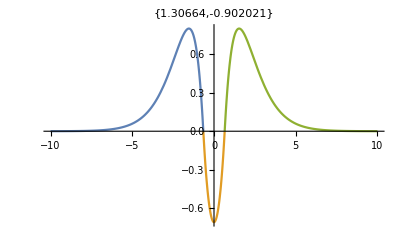

```mathematica
Plot[Evaluate@{ground[[3,1,2]][-x],ground[[4,1,2]][x]*(dgLR/dgC),ground[[3,1,2]][x]},{x,-10,10},PlotRange->All,PlotLabel->{ground[[1]],ground[[2]]}]
```

```mathematica
(dgLR/dgC) (* the central wf must be multiplied by this number to match derivatives at boundaries *)
```

0.599116

```mathematica
(2+(dgLR/dgC)^2)*ground[[3,1,1]] +Subscript[𝒱, n][-root/2,root/2]
```

-1.36249

```mathematica
(1+1+(dgLR/dgC)^2) (* the function with matching derivatives at boundaries now has this norm *)
```

2.35894

```mathematica
Sqrt[1/(1+1+(dgLR/dgC)^2)](* the global wf must be multiplied by this quantity to have it normalized *)
```

0.651091

```mathematica
root=r/.FindRoot[eCr[[2]][r]==eLRr[[1]][r],{r,2}]
```

6.04749

```mathematica
excited=Evaluate[{root,eCr[[1]][root],eC[root],eLR[root]}];
```

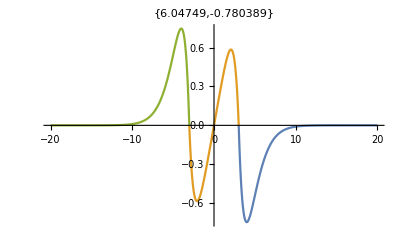

```mathematica
Plot[{excited[[4,1,2]][x],-excited[[3,2,2]][x],-excited[[4,1,2]][-x]},{x,-20,20},PlotRange->All,PlotLabel->{excited[[1]],excited[[2]]}]
```

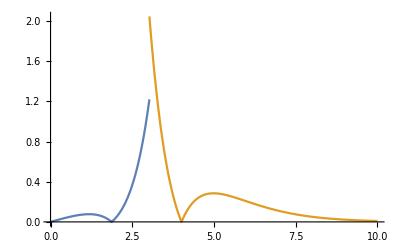

```mathematica
Plot[{Abs[D[excited[[3,1,2]][r],r]]/.r->y,Abs[D[excited[[4,1,2]][r],r]]/.r->y},{y,0,10},PlotRange->All]
```

```mathematica
(*Manipulate[
GraphicsGrid@
Partition[
(es↦Table[
Show[
Plot[{es⟦i,1⟧+(es⟦i,2⟧[x])},{x,-ℓ,ℓ},
Filling->{1->es⟦i,1⟧,2-> Bottom},PlotPoints->20,PlotRange->{le,le+ΔE}]
],
{i,1,4}
])@
eigensystem3[ℓ,𝓇,ne,0.1],
2],
{{ℓ,10,"Box Length"},10,20,1},
{{𝓇,2,"Bond Length"},1.,6.,0.5},
{{ne,40,"Number of eigenfunctions"},40,100,5},
{{le,-2,"Lowest Energy"},-10,0,0.5},
{{ΔE,3,"Energy range"},1,20,2}
]*)
```